## Cropping the image

Two methods to crop the resistor out of an image were used. The first one is more precise, as uses the whole image to process the cropping, but it’s slow for images with high dimensions. The second one resizes the image before and makes the same processing, which makes it faster but less precise.

```mathematica
resistorCrop[image_] := Module[
	{preprocess, angle, rotated, newPoints, allX, allY, minX, minY, maxX, maxY, processed, adjusted},
	adjusted = ImageAdjust @ BrightnessEqualize[image];
	(*Print[adjusted];*)
	(*Print[RemoveBackground[adjusted]];*)
	preprocess = SelectComponents[Erosion[AlphaChannel[RemoveBackground[adjusted]],10],"Count",-1];
	(*Print[preprocess];*)
	preprocess = RegionBinarize[adjusted,preprocess,0.15];
	(*Print[preprocess];*)
	processed = MorphologicalComponents[preprocess];
	angle = First @ Values[
		ComponentMeasurements[processed, "Orientation"]
	];
	rotated = ImageRotate[image, -angle, Masking->Full];
	newPoints = First @ Values[ComponentMeasurements[processed, "MinimalBoundingBox"]];
	newPoints = RotationTransform[-angle,ImageDimensions[image]/2][newPoints];
	newPoints = TranslationTransform[(ImageDimensions[rotated] - ImageDimensions[image])/2][newPoints];
	allX = newPoints[[All, 1]];
	allY = newPoints[[All, 2]];
	minX = Min[allX];
	minY = Min[allY];
	maxX = Max[allX];
	maxY = Max[allY];
	ImageTake[rotated, Ramp[ImageDimensions[rotated][[2]]-{maxY, minY}],{minX,maxX}]
]
```

```mathematica
resistorLightCrop[image_] := Module[
	{preprocess, angle, rotated, newPoints, allX, allY, minX, minY, maxX, maxY, processed, adjusted, resized, prop, fullRotated},
	resized = ImageResize[image, {500}];
	prop = ImageDimensions[image][[1]] / ImageDimensions[resized][[1]];
	adjusted = ImageAdjust @ BrightnessEqualize[resized];
	preprocess = SelectComponents[Erosion[AlphaChannel[RemoveBackground[adjusted]],10 / prop],"Count",-1];
	preprocess = RegionBinarize[adjusted,preprocess,0.15];
	processed = MorphologicalComponents[preprocess];
	angle = First @ Values[
		ComponentMeasurements[processed, "Orientation"]
	];
	rotated = ImageRotate[resized, -angle, Masking->Full];
	newPoints = First @ Values[ComponentMeasurements[processed, "MinimalBoundingBox"]];
	newPoints = RotationTransform[-angle,ImageDimensions[resized]/2][newPoints];
	newPoints = TranslationTransform[(ImageDimensions[rotated] - ImageDimensions[resized])/2][newPoints];
	allX = newPoints[[All, 1]];
	allY = newPoints[[All, 2]];
	minX = Min[allX];
	minY = Min[allY];
	maxX = Max[allX];
	maxY = Max[allY];
	fullRotated = ImageRotate[image, -angle, Masking->Full];
	ImageTake[fullRotated, Ramp[ImageDimensions[fullRotated][[2]]-{maxY * prop, minY * prop}],{minX * prop,maxX * prop}]
]
SetDirectory[NotebookDirectory[]];
DumpSave["resistorLightCrop.mx", resistorLightCrop];
ResetDirectory[];
```

## Generating the training files

If this notebook is being seen from the github repository, then is not necessary to run this section, as the images used for training are already cropped correctly.

```mathematica
assetsPath = FileNameJoin[{NotebookDirectory[], "ResistorProject", "Assets"}];
dataPath = FileNameJoin[{assetsPath, "Data"}];
croppedDataPath = FileNameJoin[{assetsPath, "ResistorData"}];
```

```mathematica
dataFiles = Map[File, FileNames[{"*.jpg","*.png"}, dataPath, Infinity]];
```

```mathematica
Map[
Module[
{img, path, directoryName},
SetDirectory[DirectoryName[FindFile @ #]];
img = Import[#];
img = resistorCrop[img];
path = FindFile[#];
directoryName = FileBaseName[DirectoryName[FindFile @ #]];
path = FileNameJoin[{croppedDataPath, directoryName}];
If[!DirectoryQ[path],CreateDirectory[path]];
Export[FileNameJoin[{path, FileBaseName[FindFile[#]]}] <> ".png",img];
]&
, dataFiles
];
```

## Generating training and test sets

```mathematica
imagesPath = FileNameJoin[{NotebookDirectory[],"ResistorProject", "Assets", "Images/"}];
dataPath = FileNameJoin[{NotebookDirectory[],"ResistorProject", "Assets", "ResistorData"}];
```

```mathematica
filesByType[type_?StringQ] := Map[
	File[#]->type&,
	FileNames[{"*.jpg", "*.png"}, FileNameJoin[{dataPath, type}]]
];
```

```mathematica
makeData[] := Flatten @ Map[
	filesByType,
	StringDrop[
		Select[FileNames["*",dataPath], DirectoryQ],
		StringLength[dataPath] + 1
	]
];
```

```mathematica
newBlurry[data_, n_] :=
Module[
	{toBlur},
	toBlur = RandomSample[data, n];
	toBlur/.(x_->y_):>GaussianFilter[x,15]->y
]
```

```mathematica
newRotated[data_, n_] := Module[
	{toRotate},
	toRotate = RandomSample[data, n];
	toRotate/.(x_->y_):>ImageRotate[x,RandomReal[{0, π}], Masking->Full]->y
]
```

```mathematica
data = RandomSample[makeData[]];
```

```mathematica
data[[1]]
```

File[/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/ResistorData/22/IMG_8076.png]→22

```mathematica
Length[data]
```

996

```mathematica
trainingData = data[[;;700]];
testData = data[[701;;]];
```

```mathematica
getAllImages[x_]:=Map[
Import[Keys[{#}][[1]]]->ToExpression[Values[{#}][[1]]]&,
x
];
```

```mathematica
trainingSet = getAllImages[trainingData];
testSet = getAllImages[testData];
```

```mathematica
trainingSet = Join[trainingSet, newBlurry[trainingSet,400 ]];
```

```mathematica
trainingSet = Join[trainingSet, newRotated[trainingSet,500 ]];
```

```mathematica
trainingSet = RandomSample[trainingSet];
```

```mathematica
newBlurry[trainingSet, 1]
```

{-Graphics-→2200}

```mathematica
newRotated[trainingSet, 1]
```

{-Graphics-→2200}

```mathematica
trainingSet[[1]]
```

-Graphics-→22

## Training models

```mathematica
cNoParameters = Classify[trainingSet, PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[cNoParameters]
```

Classifier information
Method | Logistic regression
Number of classes | 10
Number of features | 1
Number of training examples | 700
L1 regularization coefficient | 0
L2 regularization coefficient | 10.

```mathematica
cNoParametersM = ClassifierMeasurements[cNoParameters, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNoParametersM["Accuracy"]
```

0.935811

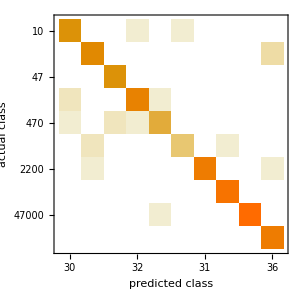

```mathematica
cNoParametersM["ConfusionMatrixPlot"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["cNoParameters.mx",cNoParameters]
ResetDirectory[];
```

{ClassifierFunction[…]}

```mathematica
images = Association[ClassifierInformation[cNoParameters, "Classes"] /. x_?IntegerQ:>(x->WolframAlpha["Resistor "<>ToString[x]<>"Ohm", "PodImages"][[2]])]
```

<|10→-Graphics-,22→-Graphics-,47→-Graphics-,100→-Graphics-,470→-Graphics-,1000→-Graphics-,2200→-Graphics-,4700→-Graphics-,47000→-Graphics-,220000→-Graphics-|>

### Other attempts for machine learning

```mathematica
cNeuralNet = Classify[trainingSet, Method->"NeuralNetwork", PerformanceGoal->"Quality", FeatureExtractor->"ImageFeatures"]
```

ClassifierFunction[…]

```mathematica
cNeuralNetM = ClassifierMeasurements[cNeuralNet, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNeuralNetM["Accuracy"]
```

0.672297

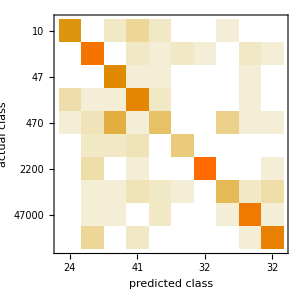

```mathematica
cNeuralNetM["ConfusionMatrixPlot"]
```

```mathematica
pNoParameters = Predict[trainingSet]
```

PredictorFunction[…]

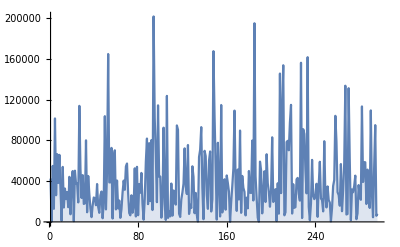

```mathematica
Show[
DiscretePlot[
Module[
{image, value},
image = Keys[testSet[[x]]];
value = Values[testSet[[x]]];
Abs[value - pNoParameters[image]]
],
{x, 1, Length[testSet], 1}
]
]
```

## Making final form

```mathematica
SetDirectory[NotebookDirectory[]];
<<cNoParameters.mx
<< resistorLightCrop.mx
```

```mathematica
form = FormPage[{"Photo"->"Image"}, Module[{result, croppedImage=resistorLightCrop[#[["Photo"]]]},
result = cNoParameters[croppedImage, {"TopProbabilities", 2}];
Rasterize @ Column[{Style[ToString[
result[[1,1]]
] <> " Ohm Resistor with probability " <> ToString[result[[1,2]]],FontFamily->"Helvetica" ,Bold,FontSize->18],
images[result[[1,1]]],
croppedImage,
Style["Other possibilities: " <> ToString[result[[2,1]]] <> " Ohm with probability "<> ToString[result[[2,2]]], FontFamily->"Helvetica", Bold, FontSize->14],
images[result[[2,1]]]
},
Alignment->Center,
Spacings->2
]]&,  AppearanceRules-><|"Title"->"Resistor image identify" , "Description"-> Column[{"Upload a picture of a resistor in a white background to figure out the resistance value.",
Style["Url: https://wolfr.am/mUtXyBEe",FontSize->20]} ],
"Styling"->Red
|>

]
```

```mathematica
URLShorten["https://www.wolframcloud.com/objects/user-e04c5037-5452-4cce-a930-8ed350d8eff0/WolfResistor"]
```

https://wolfr.am/mUtXyBEe

```mathematica
CloudDeploy[form,"WolfResistor",Permissions->"Public"]
```

CloudObject[]

```mathematica
imagen=CloudDeploy[ExportForm[-Graphics-,"PNG"],"Resis",Permissions->"Private"]
```

CloudObject[]

```mathematica
EmbeddedHTML[imagen]
```